```mathematica
LagrangePolyFactor[j_,k_,xp_]:=If[j!=k,((x-xp[[k]])/(xp[[j]]-xp[[k]])),1]
LagrangePoly[j_,xp_]:=Product[If[j!=k,((x-xp[[k]])/(xp[[j]]-xp[[k]])),1],{k,1,Length[xp]}]
```

### Equal Spacing

{-1,1}

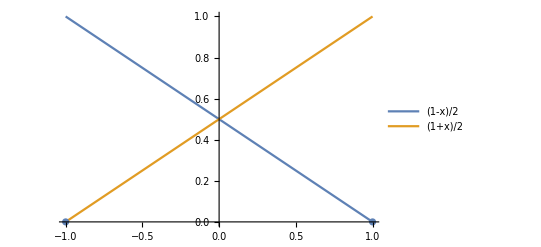

{0.35,0.65}

{-1/2,1/2}

```mathematica
order=1;
xp=Subdivide[-1,1,order]
Points=Table[{xp[[n]],0},{n,1,order+1}];
Bases=Table[LagrangePoly[n,xp],{n,1,order+1}];
Show[Plot[Bases,{x,-1,1},PlotRange->Full,PlotLegends->"Expressions"],ListPlot[Points]]
NumberForm[Bases/.x->0.3,14]
NumberForm[D[Bases,x]/.x->0.3,14]
```

### Gauss-Lobatto Spacing

{-1.,1.}

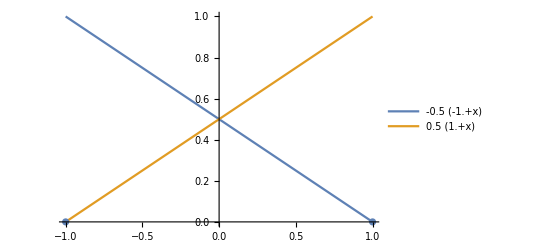

{0.35,0.65}

{-0.5,0.5}

```mathematica
GaussLobattoPointsWeights=ResourceFunction["ModifiedGaussianQuadratureWeights"]["Lobatto",order+1];
xp=Table[GaussLobattoPointsWeights[[n,1]],{n,1,order+1}]
Points=Table[{xp[[n]],0},{n,1,order+1}];
Bases=Table[LagrangePoly[n,xp],{n,1,order+1}];
Show[Plot[Bases,{x,-1,1},PlotRange->Full,PlotLegends->"Expressions"],ListPlot[Points]]
NumberForm[Bases/.x->0.3,14]
NumberForm[D[Bases,x]/.x->0.3,14]
```

```mathematica
NumberForm[MatrixForm[GaussLobattoPointsWeights=ResourceFunction["ModifiedGaussianQuadratureWeights"]["Lobatto",9]],14]
```

(-1. | 0.027777777777777
-0.89975799541146 | 0.16549536156081
-0.67718627951074 | 0.27453871250016
-0.36311746382618 | 0.34642851097305
-4.4408920985006×10^-16 | 0.37151927437642
0.36311746382618 | 0.34642851097305
0.67718627951074 | 0.27453871250016
0.89975799541146 | 0.16549536156081
1. | 0.027777777777778)

```mathematica
1/.066666666666665
```

15.

```mathematica
1/"0.37847495629785"
```

2.64218

```mathematica
1/0.55485837703549
```

1.80226

## 3 D product

```mathematica
GLp1=ResourceFunction["ModifiedGaussianQuadratureWeights"]["Lobatto",order+2];
NumberForm[evalPoints={0.31415,-0.161803,0.69314},14]
```

{0.31415,-0.161803,0.69314}

```mathematica
TPBasis3[a_,b_,c_,ξ0_,ξ1_,ξ2_]:=(Bases[[a]]/.x->ξ0)(Bases[[b]]/.x->ξ1)(Bases[[c]]/.x->ξ2)
DTPBasis3[a_,b_,c_,ξ0_,ξ1_,ξ2_]:={ D[TPBasis3[a,b,c,x,ξ1,ξ2],x]/.x->ξ0,
									D[TPBasis3[a,b,c,ξ0,x,ξ2],x]/.x->ξ1,
									D[TPBasis3[a,b,c,ξ0,ξ1,x],x]/.x->ξ2}
```

```mathematica
TPBasis3[2,1,1,ξ0,ξ1,ξ2]
D[TPBasis3[2,1,1,ξ0,ξ1,ξ2],ξ0]
```

0.125 (1.+ξ0) (-1.+ξ1) (-1.+ξ2)

0.125 (-1.+ξ1) (-1.+ξ2)

```mathematica
Baselines=Table[TPBasis3[a,b,c,evalPoints[[1]],evalPoints[[2]],evalPoints[[3]]],
{a,1,order+1},{b,1,order+1},{c,1,order+1}];
Dimensions[Baselines]
NumberForm[Chop[Baselines,10^-14],14]
```

{2,2,2}

{{{0.030564122401949,0.16864152448555},{0.022050860348051,0.12166849276445}},{{0.058563594743051,0.32313225836945},{0.042251422506949,0.23312772438055}}}

```mathematica
Bases
```

{-0.5 (-1.+x),0.5 (1.+x)}

```mathematica
GradientBaselines=Table[DTPBasis3[a,b,c,evalPoints[[1]],evalPoints[[2]],evalPoints[[3]]],
{a,1,order+1},{b,1,order+1},{c,1,order+1}];
Dimensions[GradientBaselines]
NumberForm[Chop[GradientBaselines,10^-14],14]
```

{2,2,2,3}

{{{{-0.0445638585725,-0.026307491375,-0.09960282344375},{-0.2458868914275,-0.145155008625,0.09960282344375}},{{-0.0321511414275,0.026307491375,-0.07185967655625},{-0.1773981085725,0.145155008625,0.07185967655625}}},{{{0.0445638585725,-0.050407508625,-0.19084792655625},{0.2458868914275,-0.278129991375,0.19084792655625}},{{0.0321511414275,0.050407508625,-0.13768957344375},{0.1773981085725,0.278129991375,0.13768957344375}}}}